```mathematica
P[h_]:={{26h/35,9h/35,11h^2/105,-13h^2/210},
{9h/35,26h/35,13h^2/210,-11h^2/105},
{11h^2/105,13h^2/210,2h^3/105,-h^3/70},
{-13h^2/210,-11h^2/105,-h^3/70,2h^3/105}};
Q[h_]:={{-12/(5h),12/(5h),-11/5,-1/5},
{12/(5h),-12/(5h),1/5,11/5},
{-1/5,1/5,-4h/15,h/15},
{-1/5,1/5,h/15,-4h/15}};
```

```mathematica
(* make the entire P or Q matrix *)
makePorQ[N_,PorQ_]:=Module[{res=ConstantArray[0,{2N,2N}]},
res[[{1,N,N+1},{1,N,N+1}]]+=PorQ[[{2,3,4},{2,3,4}]];
Do[res[[{i,i+1,N+i,N+i+1},{i,i+1,N+i,N+i+1}]]+=PorQ,{i,1,N-2}];
res[[{N-1,2N-1,2N},{N-1,2N-1,2N}]]+=PorQ[[{1,3,4},{1,3,4}]];
res]
```

```mathematica
(* integrate the square of a function in an interval *)
intsq[ψ0_,ψh_,ψdot0_,ψdoth_,h_]:=1/35 (13 ψ0^2+9 ψ0 ψh+13 ψh^2) h+1/210 (22 ψ0 ψdot0-13 ψ0 ψdoth+13 ψdot0 ψh-22 ψdoth ψh) h^2+1/210 (2 ψdot0^2-3 ψdot0 ψdoth+2 ψdoth^2) h^3;
```

```mathematica
(* normalize an eigenvector of the Hamiltonian *)
normal[ψ_,N_]:=Module[{},res=0;
res+=intsq[0,ψ[[1]],ψ[[N]],ψ[[N+1]],1/N];
Do[res+=intsq[ψ[[i]],ψ[[i+1]],ψ[[N+i]],ψ[[N+i+1]],1/N],{i,1,N-2}];
res+=intsq[ψ[[N-1]],0,ψ[[2N-1]],ψ[[2N]],1/N];
1/Sqrt[res]]
```

```mathematica
(* use values and first derivatives to get the value at a specified location *)
A[x0_,v0_,xh_,vh_,h_]:=2(x0-xh)h^-3+(v0+vh)h^-2;
B[x0_,v0_,xh_,vh_,h_]:=3(xh-x0)h^-2-(2v0+vh)h^-1;
interp[ψ0_,ψh_,ψdot0_,ψdoth_,h_,x_]:=Module[
{Aψ=A[ψ0,ψdot0,ψh,ψdoth,h],Bψ=B[ψ0,ψdot0,ψh,ψdoth,h]},
ψ0+ψdot0 x+Bψ x^2+Aψ x^3];
```

```mathematica
(* render a piecewise cubic function from a renormalize eigenvector *)
render[ψ_,N_,x_]:=Module[{i=IntegerPart[x*N]},
If[N==1,res=interp[0,0,ψ[[1]],ψ[[2]],1,x],
If[i==N,i-=1,];
If[i==0,res=interp[0,ψ[[1]],ψ[[N]],ψ[[N+1]],1/N,x-i/N],];
If[0<i<N-1,res=interp[ψ[[i]],ψ[[i+1]],ψ[[N+i]],ψ[[N+i+1]],1/N,x-i/N],];
If[i==N-1,res=interp[ψ[[N-1]],0,ψ[[2N-1]],ψ[[2N]],1/N,x-i/N],]];
res]
```

```mathematica
(* N = 1 case *)
```

```mathematica
P1=P[1]
```

{{26/35,9/35,11/105,-13/210},{9/35,26/35,13/210,-11/105},{11/105,13/210,2/105,-1/70},{-13/210,-11/105,-1/70,2/105}}

```mathematica
Q1=Q[1]
```

{{-12/5,12/5,-11/5,-1/5},{12/5,-12/5,1/5,11/5},{-1/5,1/5,-4/15,1/15},{-1/5,1/5,1/15,-4/15}}

```mathematica
PP1=P1[[{3,4},{3,4}]];MatrixPlot[PP1];
```

```mathematica
QQ1=Q1[[{3,4},{3,4}]];MatrixPlot[QQ1];
```

```mathematica
HH1=-Inverse[PP1].QQ1;MatrixPlot[HH1];
```

```mathematica
{EE1,ψψ1}=Eigensystem[HH1];
```

```mathematica
NN1={√210,√30};(* yesterday's results *)
```

```mathematica
MatrixPlot[Sign[ψψ1[[All,1]]]*NN1*ψψ1];
```

```mathematica
Plot[{√2 Sin[Pi x],-√30 (-1+x) x},{x,0,1},PlotLegends->Placed[{"Exact","N=1"},{Center,Bottom}]];
```

```mathematica
Plot[{√2 Sin[2Pi x],√210 x (1-3 x+2 x^2),},{x,0,1}];
```

```mathematica
(* N = 2 case *)
```

```mathematica
P2=P[1/2]
```

{{13/35,9/70,11/420,-13/840},{9/70,13/35,13/840,-11/420},{11/420,13/840,1/420,-1/560},{-13/840,-11/420,-1/560,1/420}}

```mathematica
Q2=Q[1/2]
```

{{-24/5,24/5,-11/5,-1/5},{24/5,-24/5,1/5,11/5},{-1/5,1/5,-2/15,1/30},{-1/5,1/5,1/30,-2/15}}

```mathematica
(* PP2=ConstantArray[0,{4,4}];PP2[[{1,2,3},{1,2,3}]]+=P2[[{2,3,4},{2,3,4}]];
PP2[[{1,3,4},{1,3,4}]]+=P2[[{1,3,4},{1,3,4}]]; *)
PP2=makePorQ[2,P2];MatrixPlot[PP2];
```

```mathematica
(* QQ2=ConstantArray[0,{4,4}];QQ2[[{1,2,3},{1,2,3}]]+=Q2[[{2,3,4},{2,3,4}]];
QQ2[[{1,3,4},{1,3,4}]]+=Q2[[{1,3,4},{1,3,4}]]; *)
QQ2=makePorQ[2,Q2];
MatrixPlot[QQ2];
```

```mathematica
HH2=-Inverse[PP2].QQ2;MatrixPlot[HH2];
```

```mathematica
{EE2,ψψ2}=Eigensystem[HH2]
```

{{168,24/65 (141+16 √51),40,-24/65 (-141+16 √51)},{{0,1,1,1},{1/39 (-5+√51),-1,0,1},{0,1,-1,1},{1/39 (-5-√51),-1,0,1}}}

```mathematica
N[EE2/(Range[4,1,-1]Pi)^2,16]
```

{1.063872428244547,1.06106808590776,1.013211836423378,1.000260625158498}

```mathematica
NN2=Table[normal[ψψ2[[i]],2],{i,4}]
```

{2 √210,1/(√(1/420+(5-√51)/1260+(-5+√51)^2/4095)),2 √30,1/(√(1/420+(-5-√51)^2/4095+(5+√51)/1260))}

```mathematica
MatrixPlot[Sign[ψψ2[[All,2]]]*NN2*ψψ2];
```

```mathematica
plotψ2[i_]:=Plot[{render[Sign[ψψ2[[i,2]]]*NN2[[i]]*ψψ2[[i]],2,x],√2 Sin[(5-i)Pi x]},{x,0,1}];
```

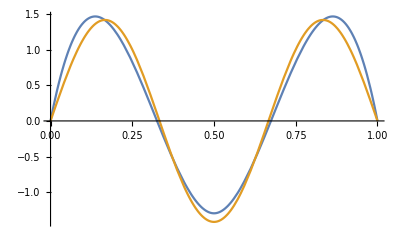

```mathematica
plotψ2[2]
```

```mathematica
(* N = 4 case *)
```

```mathematica
P4=P[1/4]
```

{{13/70,9/140,11/1680,-13/3360},{9/140,13/70,13/3360,-11/1680},{11/1680,13/3360,1/3360,-1/4480},{-13/3360,-11/1680,-1/4480,1/3360}}

```mathematica
Q4=Q[1/4]
```

{{-48/5,48/5,-11/5,-1/5},{48/5,-48/5,1/5,11/5},{-1/5,1/5,-1/15,1/60},{-1/5,1/5,1/60,-1/15}}

```mathematica
PP4=makePorQ[4,P4];MatrixPlot[PP4];
```

```mathematica
QQ4=makePorQ[4,Q4];MatrixPlot[QQ4];
```

```mathematica
HH4=-Inverse[PP4].QQ4;MatrixPlot[HH4];
```

```mathematica
{EE4,ψψ4}=Eigensystem[N[HH4,16]];
```

```mathematica
N[EE4/(Range[8,1,-1]Pi)^2,16]
```

{1.063872428244547,1.133355574736498,1.06106808590776,1.022089351875688,1.013211836423378,1.001854866997621,1.000260625158498,1.000006350367587}

```mathematica
NN4=Table[normal[ψψ4[[i]],4],{i,8}];
```

```mathematica
MatrixPlot[Sign[ψψ4[[All,4]]]*NN4*ψψ4];
```

```mathematica
plotψ4[i_]:=Plot[{√2 Sin[(9-i)Pi x],render[Sign[ψψ4[[i,4]]]*NN4[[i]]*ψψ4[[i]],4,x]},{x,0,1}];
```

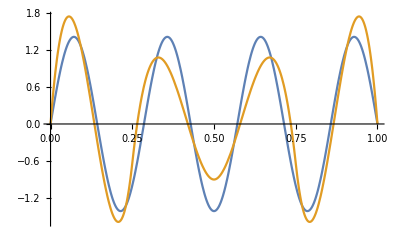

```mathematica
plotψ4[2]
```

```mathematica
(* N = 8 case *)
```

```mathematica
P8=P[1/8]
```

{{13/140,9/280,11/6720,-13/13440},{9/280,13/140,13/13440,-11/6720},{11/6720,13/13440,1/26880,-1/35840},{-13/13440,-11/6720,-1/35840,1/26880}}

```mathematica
Q8=Q[1/8]
```

{{-96/5,96/5,-11/5,-1/5},{96/5,-96/5,1/5,11/5},{-1/5,1/5,-1/30,1/120},{-1/5,1/5,1/120,-1/30}}

```mathematica
PP8=makePorQ[8,P8];MatrixPlot[PP8];
```

```mathematica
QQ8=makePorQ[8,Q8];MatrixPlot[QQ8];
```

```mathematica
HH8=-Inverse[N[PP8,16]].N[QQ8,16];MatrixPlot[HH8];
```

```mathematica
{EE8,ψψ8}=Eigensystem[HH8];
```

```mathematica
NN8=Table[normal[ψψ8[[i]],8],{i,16}];
```

```mathematica
MatrixPlot[Sign[ψψ8[[All,8]]]*NN8*ψψ8];
```

```mathematica
plotψ8[i_]:=Plot[{√2 Sin[(17-i)Pi x],render[Sign[ψψ8[[i,8]]]*NN8[[i]]*ψψ8[[i]],8,x]},{x,0,1}];
```

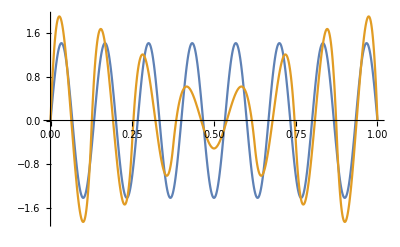

```mathematica
plotψ8[2]
```

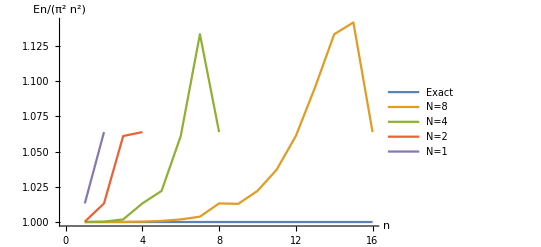

```mathematica
ListLinePlot[{ConstantArray[1,16],
Reverse[EE8]/(Range[16]Pi)^2,Reverse[EE4]/(Range[8]Pi)^2,
Reverse[EE2]/(Range[4]Pi)^2,Reverse[EE1]/(Range[2]Pi)^2},
AxesLabel->{n,En/(n π)^2},
PlotLegends->Placed[{"Exact","N=8","N=4","N=2","N=1"},{Left,Top}]]
```

```mathematica
getlist[n_]:=Module[{res={√2 Sin[n Pi x],render[Sign[ψψ8[[17-n,8]]]*NN8[[17-n]]*ψψ8[[17-n]],8,x]}},
res]
```

```mathematica
(* need to comment out some lines as n increases *)
plotψs[n_]:=Module[{},
Plot[{√2 Sin[n Pi x],render[Sign[ψψ8[[17-n,8]]]*NN8[[17-n]]*ψψ8[[17-n]],8,x],render[Sign[ψψ4[[9-n,4]]]*NN4[[9-n]]*ψψ4[[9-n]],4,x],render[Sign[ψψ2[[5-n,2]]]*NN2[[5-n]]*ψψ2[[5-n]],2,x](*,render[Sign[ψψ1[[3-n,1]]]*NN1[[3-n]]*ψψ1[[3-n]],1,x]*)},{x,0,1}(*,PlotLegends->Placed[{"Exact","N=8","N=4","N=2","N=1"},{Center,Bottom}]*)]]
```

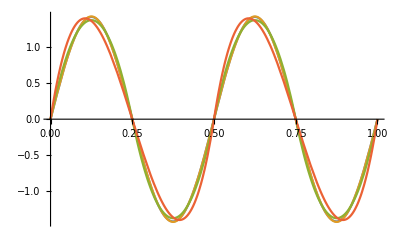

```mathematica
plotψs[4]
```